```mathematica
ClearSystemCache[]
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

## Annihilations

```mathematica
TEMP = ((1*^3*1*^-9)/(1.16*^4)); (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11;(*Grav Constant*)
```

## Interpolating Functions

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)

NSMass=   Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *)
```

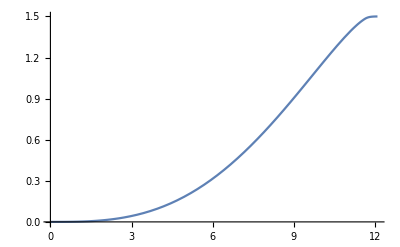

```mathematica
Plot[NSMass[x], {x, rMin, rMax}]
```